```mathematica
SetDirectory[NotebookDirectory[]];
```

# T_scaling

## data

```mathematica
fpi=Flatten[Import["./IR0p01/LPA_Tscaling_mub0_v2/buffer/mSigma.dat"]];
T0=Flatten[Import["./IR0p01/LPA_Tscaling_mub0_v2/buffer/TMeV.dat"]];
t=-(T0-T0[[1]])/T0[[1]];
datamub0=Transpose[{Log[-t[[2;;Length[t]]]],Log[1/fpi[[2;;Length[t]]]]}];
b1mub0=Transpose[{Log[-t[[2;;Length[t]-2]]],-Flatten[Table[FindFit[datamub0[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T0]-2}]]}];
fpi=Flatten[Import["./IR0p001/LPA_Tscaling_mub0/buffer/mSigma.dat"]];
T0=Flatten[Import["./IR0p001/LPA_Tscaling_mub0/buffer/TMeV.dat"]];
t=-(T0-T0[[1]])/T0[[1]];
datamub0=Transpose[{Log[-t[[2;;Length[t]]]],Log[1/fpi[[2;;Length[t]]]]}];
b1mub02=Transpose[{Log[-t[[2;;Length[t]-2]]],-Flatten[Table[FindFit[datamub0[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T0]-2}]]}];

fpi=Flatten[Import["./IR0p01/LPA_Tscaling_TCP/buffer/mSigma.dat"]];
T0=Flatten[Import["./IR0p01/LPA_Tscaling_TCP/buffer/TMeV.dat"]];
t=-(T0-T0[[1]])/T0[[1]];
datamub0=Transpose[{Log[-t[[2;;Length[t]]]],Log[1/fpi[[2;;Length[t]]]]}];
b1TCP=Transpose[{Log[-t[[2;;Length[t]-2]]],-Flatten[Table[FindFit[datamub0[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T0]-2}]]}];

fpi=Flatten[Import["./IR0p001/LPA_Tscaling_TCP/buffer/mSigma.dat"]];
T0=Flatten[Import["./IR0p001/LPA_Tscaling_TCP/buffer/TMeV.dat"]];
t=-(T0-T0[[1]])/T0[[1]];
datamub0=Transpose[{Log[-t[[2;;Length[t]]]],Log[1/fpi[[2;;Length[t]]]]}];
b1TCP2=Transpose[{Log[-t[[2;;Length[t]-2]]],-Flatten[Table[FindFit[datamub0[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T0]-2}]]}];
```

## Plot

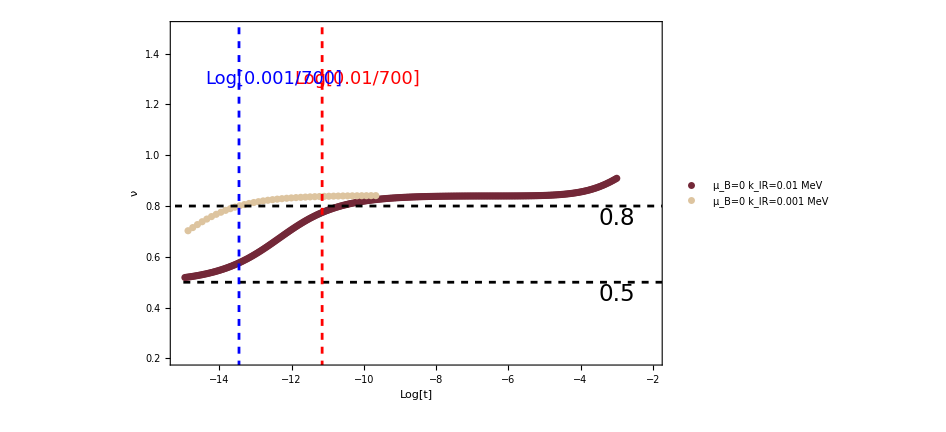

```mathematica
plotT=Show[ListPlot[{b1mub0,b1mub02},
Frame->True,FrameLabel->{Style["Log[t]",25,FontFamily->"Times",Black],Style["ν",25,FontFamily->"Times",Black]},
PlotStyle->Table[Directive[ColorData["RedBlueTones"][i],AbsoluteThickness[3.]],{i,0,1,0.4}],PlotStyle->10,
PlotLegends->Placed[LineLegend[{"μ_B=0 k_IR=0.01 MeV","μ_B=0 k_IR=0.001 MeV"},LabelStyle->16],{0.7,0.65}],
PlotRange->{{-15.1,-2},{0.2,1.5}},AxesOrigin->{-15.1,0.3},FrameTicksStyle->Directive[15,Black]],
ListLinePlot[{{-16,0.8},{10,0.8}},PlotStyle->{Black,Dashed}],ListLinePlot[{{-15,0.5},{10,0.5}},PlotStyle->{Black,Dashed}],ListLinePlot[{{-11.1563,0.},{-11.1563,10}},PlotStyle->{Red,Dashed}],ListLinePlot[{{-13.4588,0.},{-13.4588,10}},PlotStyle->{Blue,Dashed}],ImageSize->700,Background->None,Epilog->{Text[Style["0.8",23],{-3,0.75}],Text[Style["0.5",23],{-3,0.45}],Text[Style["Log[0.01/700]",18,Red],{-10.2,1.3}],Text[Style["Log[0.001/700]",18,Blue],{-12.5,1.3}]}]
```

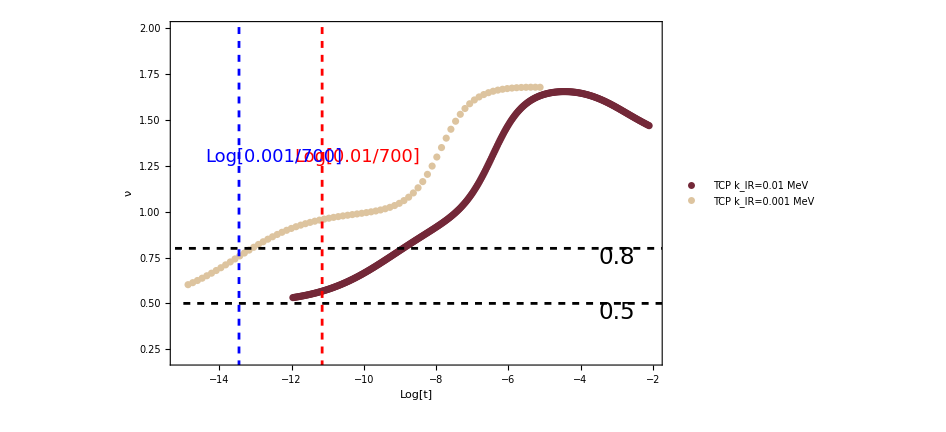

```mathematica
plotT=Show[ListPlot[{b1TCP,b1TCP2},
Frame->True,FrameLabel->{Style["Log[t]",25,FontFamily->"Times",Black],Style["ν",25,FontFamily->"Times",Black]},
PlotStyle->Table[Directive[ColorData["RedBlueTones"][i],AbsoluteThickness[3.]],{i,0,1,0.4}],PlotStyle->10,
PlotLegends->Placed[LineLegend[{"TCP k_IR=0.01 MeV","TCP k_IR=0.001 MeV"},LabelStyle->16],{0.7,0.65}],
PlotRange->{{-15.1,-2},{0.2,2}},AxesOrigin->{-15.1,0.3},FrameTicksStyle->Directive[15,Black]],
ListLinePlot[{{-16,0.8},{10,0.8}},PlotStyle->{Black,Dashed}],ListLinePlot[{{-15,0.5},{10,0.5}},PlotStyle->{Black,Dashed}],ListLinePlot[{{-11.1563,0.},{-11.1563,10}},PlotStyle->{Red,Dashed}],ListLinePlot[{{-13.4588,0.},{-13.4588,10}},PlotStyle->{Blue,Dashed}],ImageSize->700,Background->None,Epilog->{Text[Style["0.8",23],{-3,0.75}],Text[Style["0.5",23],{-3,0.45}],Text[Style["Log[0.01/700]",18,Red],{-10.2,1.3}],Text[Style["Log[0.001/700]",18,Blue],{-12.5,1.3}]}]
```

```mathematica
Log[0.001/700]
```

-13.4588